# Logic-“Digital System” Related

Dali Lai

1. Combinational Circuit-logic gate

By combining different logic gates (AND, NAND, OR...etc.), the circuit can output the desired output while receiving a certain input. 
In programming, know as truth table (but more complicated). 

For example the Karnaugh map (k-map) for X || Y:

```mathematica
WebImageSearch[#,"Images",Method->"Google"]&["or gate"][[4]]
```

```mathematica
Grid[MapThread[Prepend,{Prepend[BooleanTable[x||y,{x},{y}],{"1","0"}],{"x/y","1","0"}}],Frame->All]
```

x/y | 1 | 0
1 | True | True
0 | True | False

To prove it, let’s simulate the logic gate OR with 2 inputs in SystemModeler, a software that can model and simulate circuit behaior and others more. 

-Graphics-

```mathematica
orgate=SystemModelPlot[SystemModelSimulate[-Graphics-,{0,0.5}],{"pulse1.y","pulse2.y"},PlotStyle->Dashed,PlotLegends->{"50% duty cycle step","80% duty cycle step"},PlotStyle->Thick]
Show[orgate,SystemModelPlot[SystemModelSimulate[-Graphics-,{0,0.5}],{"orGate1.y"},PlotLegends->{"OR gate output"},PlotStyle->{Red,Thin}]]
```

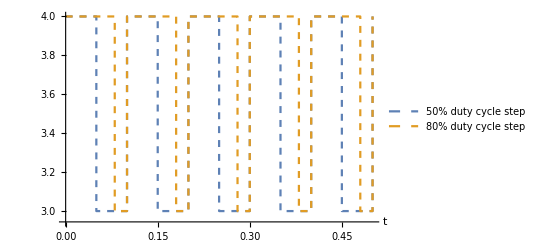

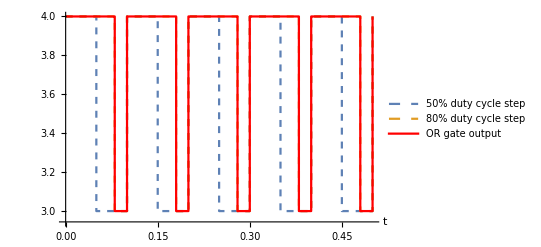

Another example for XOR gate:

```mathematica
WebImageSearch[#,"Images",Method->"Google"]&["xor gate"][[5]]
```

-Graphics-

```mathematica
Grid[MapThread[Prepend,{Prepend[BooleanTable[x⊻y,{x},{y}],{"1","0"}],{"x/y","1","0"}}],Frame->All]
```

x/y | 1 | 0
1 | False | True
0 | True | False

```mathematica
xorgate=SystemModelPlot[SystemModelSimulate[-Graphics-,{0,0.5}],{"pulse1.y","pulse2.y"},PlotStyle->Dashed,PlotLegends->{"50% duty cycle step","80% duty cycle step"},PlotStyle->Thick]
Show[xorgate,SystemModelPlot[SystemModelSimulate[-Graphics-,{0,0.5}],{"xorGate1.y"},PlotLegends->{"XOR gate output"},PlotStyle->{Red,Thin}]]
```

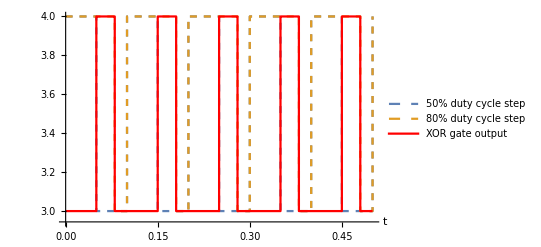

2. Combinational Circuit-multiple inputs/gates

As the tittle indicated, this is about the combination of logic gates, and its application.  
Here are some examples about the combinational circuit examples that are more than 2 inputs and hard to see the result just by hand.
Lets say a 4 inputs combinational circuit:

```mathematica
gate4=SystemModelPlot[SystemModelSimulate[-Graphics-,{0,0.5}],{"pulse1.y","pulse2.y","pulse3.y","pulse4.y"},PlotStyle->Dashed,PlotLegends->{"50% duty cycle step (A)","80% duty cycle step (B)","30% duty cycle step (C)","40% duty cycle step (D)"},PlotStyle->Thick]
Show[gate4,SystemModelPlot[SystemModelSimulate[-Graphics-,{0,0.5}],{"xorGate1.y"},PlotLegends->{"output"},PlotStyle->{Black,Thin}]]
```

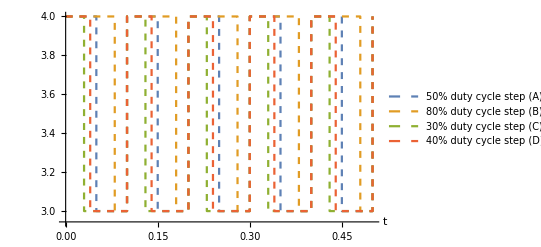

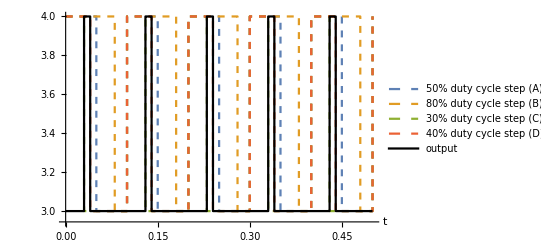

Notice that these kind of combinational circuit are a bit hard to know the truth table just from head directly, but still can be written the whole expression by hand (and will always be)
By writing the whole expression by hand, one can get the output logic expression is equal to 
((A∨B∨C)⊼(C))⊻(C⊽D)
And... it’s still not very clear what the output is.

```mathematica
BooleanMinimize[((A∨B∨C)⊼(C))⊻(C⊽D)]
```

!C&&D

The whole logic expression, most of the time (not take into account timing hazard), can be simplified using different axioms of switching algebra , Demorgan’s law...etc. 
Just check the K-map to make sure they are the same thing.

```mathematica
Grid[MapThread[Prepend,{Prepend[BooleanTable[((A∨B∨CC)⊼(CC))⊻(CC⊽DD),{A,B},{CC,DD}],{"11","10","01","00"}],{"CD/AB","11","10","01","00"}}],Frame->All]
```

CD/AB | 11 | 10 | 01 | 00
11 | False | False | True | False
10 | False | False | True | False
01 | False | False | True | False
00 | False | False | True | False

```mathematica
BooleanTable[!CC&&DD,{CC,DD}]//TraditionalForm
```

```mathematica
{False,False,True,False}
```

Can confirm that the output of this logic circuit won’t depends on A and B at least in simulation and most of the time. 

Takeaway: Timing diagram (the graph with input and output), K-map (pretty much the same as truth table), logic expression are ways to represent the behavior of the combinational circuit, depends on how one wants to represent, one can be more useful than others, but they are all interchangeable.

## 3. Demorgan’s Law

“A logically equivalent circuit can be formed by taking the dual of the operator(s) and complementing all the inputs and outputs.”
Demorgan’s law is useful when minimizing logic expression as well as in practice, let’s say to perform a !&& expression, and the only IC chip left in the lab are AND, OR, NOT (know as inverter), of course one can build an AND gate combine with a NOT gate, however, it is preferable using least amount of IC chips possible due to speed (propagation delay) and cost in practice.    

Example for proof (will skip circuit simulation since we already know K-map represents the result):

#### (A&&B)’≡A’+B’

```mathematica
Grid[MapThread[Prepend,{Prepend[BooleanTable[A⊼B,{A},{B}],{"1","0"}],{"A/B","1","0"}}],Frame->All]
```

A/B | 1 | 0
1 | False | True
0 | True | True

```mathematica
Grid[MapThread[Prepend,{Prepend[BooleanTable[!A∨!B,{A},{B}],{"1","0"}],{"A/B","1","0"}}],Frame->All]
```

A/B | 1 | 0
1 | False | True
0 | True | True

Also,

```mathematica
SatisfiableQ[!(a&&b)&&(!a||!b),{a,b}]
```

```mathematica
True
```

## 4. Applications

Knowing that giving a logic expression, one can get a truth table (or k-map), but this can go other way around. 
Let’s say one wants to only let the output be on when a specific input set is engaged, for example like a digital password, displaying numbers or words...etc.
Knowing the logic expression makes programming on FPGA board much simpler since just implementing a logic expression is much easy to understand and debug than hard coding 2^8 states.

```mathematica
Manipulate[Grid[MapThread[Prepend,{Prepend[BooleanTable[BooleanFunction[FromDigits[{q,w,e,r,t,y,u,i},2],{a,b,c}],{a},{b,c}],{"11","10","01","00"}],{"bc/a","1","0"}}],Frame->All]
BooleanFunction[FromDigits[{q,w,e,r,t,y,u,i},2],{a,b,c}],{{q,0,"111"},0,1,1},{{w,0,"110"},0,1,1},{{e,0,"101"},0,1,1},{{r,0,"100"},0,1,1},{{t,0,"011"},0,1,1},{{y,0,"010"},0,1,1},{{u,0,"001"},0,1,1},{{i,0,"000"},0,1,1}]
```

## 5. Neat Example/ Future function/ Conclusion

What if there are more than 4 variables? What would the map be like? 
Import["C:\Users\dali7\Pictures\lec-5-combinational-logic-kmaps2-9-638.jpg"]
-Graphics-
So a 3D K-map will be used, which unsurprisingly it’s kind of hard to visualize, then a 3D K-map which the operator can rotate the K-map planes around and visualize will be helpful for understanding especially for students who first time finding the Min/Max terms more than 4 variables K-map by hand. 

For the application aspect, most of the time, FPGA board programmers only knows when the output should be on when a specific set of input is received, so finding the logic expression is the main point. 
Below is a neat example, 4 variables k-map done by Mariusz Jankowski, found on Wolfram Demonstrations Projects.
Just by inputting certain ON set on the K-map, an logic expression will appear.

```mathematica
toMinterm[{r_,c_}]:=(4#[[1]]+#[[2]]&)[{3-r,c}/.{2->3,3->2}];
circ[{x_,y_}]:=Disk[{y+0.5,x+0.5},0.15];
labels={"00","01","11","10"};
grid=Graphics[{Line@Table[{{i,0},{i,4}},{i,0,4,1}],
Line@Table[{{0,i},{4,i}},{i,0,4,1}],Table[Text[labels[[3-i+1]],{-0.25,i+0.25}],{i,{0,1,3,2}}],Table[Text[labels[[i+1]],{i+0.75,4.25}],{i,{0,1,3,2}}],Line[{{0,4},{-0.75,4.75}}],Text[Style[TraditionalForm[a b],16],{-0.5,4.}],Text[Style[TraditionalForm[c d],16],{0.,4.5}]},ImageSize->{200,200}] ;
Manipulate[
Column[{
ClickPane[Dynamic@Show[{
If[Length[plist]==0,grid,{grid,Graphics[{Black,Table[circ[plist[[i]]],{i,1,Length[plist],1}]}]}]},ImageSize->{200,200}],
(plist=If[MemberQ[plist,Reverse@Floor[#]],DeleteCases[plist,Reverse@Floor[#]],Append[plist,Reverse@Floor[#]]])&],
Panel[Text@TraditionalForm@Dynamic@BooleanMinimize@BooleanMinterms[toMinterm/@plist,{a,b,c,d}],BaseStyle->{FontSize->16},ImageSize->{380,100},Alignment->{Center,Center}]},Spacings->2,Alignment->Center],
{{plist,{{0,1},{1,1},{1,2},{2,1},{2,2}}},ControlType->None},
SaveDefinitions->True]
```

Combining the ability of simulating circuit as well as truth table , one can do some basic digital design with these tools and functions.